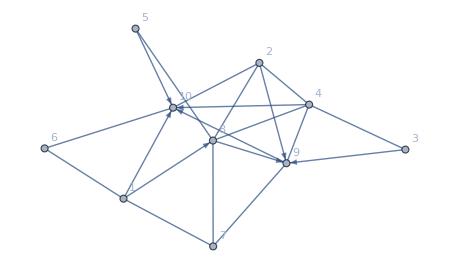

```mathematica
randomGraph=RandomWeightedMixedGraph[{10,20},0.4,RandomReal[]&,VertexLabels->Automatic]
```

```mathematica
weightedAdjacencyMatrix=WeightedAdjacencyMatrix[randomGraph]
```

SparseArray[…]

```mathematica
weightedAdjacencyMatrix[[5,10]]
```

0.363074

```mathematica
AnnotationValue[{randomGraph,5->10},EdgeWeight]
```

0.363074

c_e, the cost of traversing an edge e, ix equal to weightedAdjacencyMatrix[vertex1,vertex2]. The order does not matter if the edge is undirected but if its is undirected the order matters. x_ij is whether the edge with i and j is traversed and 0 by default. It can 0 or 1, or more such as 2,3,4,etc.

```mathematica
UndirectedEdgeWeightFromVertices[graph_?GraphQ,vertexA_,vertexB_]:=WeightedAdjacencyMatrix[graph][[vertexA,vertexB]]
```

```mathematica
UndirectedEdgeWeightFromEdge[graph_?GraphQ,edge_UndirectedEdge]:=AnnotationValue[{graph,edge},EdgeWeight]
```

```mathematica
DirectedArcWeightFromVertices[graph_?GraphQ,vertexA_,vertexB_]:=Max[{WeightedAdjacencyMatrix[graph][[vertexA,vertexB]],WeightedAdjacencyMatrix[graph][[vertexB,vertexA]]}]
```

```mathematica
DirectedArcWeightFromArc[graph_?GraphQ,edge_DirectedEdge]:=AnnotationValue[{graph,edge},EdgeWeight]
```

```mathematica
g=-Graphics-;
```

```mathematica
VertexOutComponent[g,{1},1]
```

{1,2,5,6}

```mathematica
Rest@VertexOutComponent[g,{4},1]
```

{5,9}

```mathematica
VertexInComponent[g,{1},1]
```

{1}

```mathematica
Rest@VertexInComponent[g,{4},1]
```

{3}

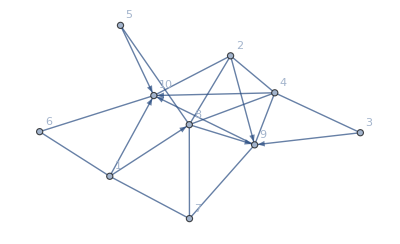

```mathematica
randomGraph
```

```mathematica
EdgeList[randomGraph]
```

{1->8,1->10,2->9,3->9,4->10,5->10,8->9,9->10,1<->6,1<->7,2<->4,2<->8,2<->10,3<->4,4<->8,4<->9,5<->8,6<->10,7<->8,7<->9}

```mathematica
AssociationMap[f↦]
```

```mathematica
{a,b,c,d,e,f}.{1<->a,1<->2,1<->3,1<->4,1<->5,1<->6}
```

b (1<->2)+c (1<->3)+d (1<->4)+e (1<->5)+f (1<->6)+a (1<->a)

```mathematica
{a,b,c,d,e,f}.({1<->a,1<->2,1<->3,1<->4,1<->5,1<->6})/.{1<->6->0}
```

b (1<->2)+c (1<->3)+d (1<->4)+e (1<->5)+a (1<->a)

```mathematica
EdgeList[randomGraph]
```

{1->8,1->10,2->9,3->9,4->10,5->10,8->9,9->10,1<->6,1<->7,2<->4,2<->8,2<->10,3<->4,4<->8,4<->9,5<->8,6<->10,7<->8,7<->9}

```mathematica
EdgeList[randomGraph,_DirectedEdge]
```

{1->8,1->10,2->9,3->9,4->10,5->10,8->9,9->10}

```mathematica
startNodes={#,First[#]}&/@EdgeList[randomGraph,_DirectedEdge]
```

{{1->8,1},{1->10,1},{2->9,2},{3->9,3},{4->10,4},{5->10,5},{8->9,8},{9->10,9}}

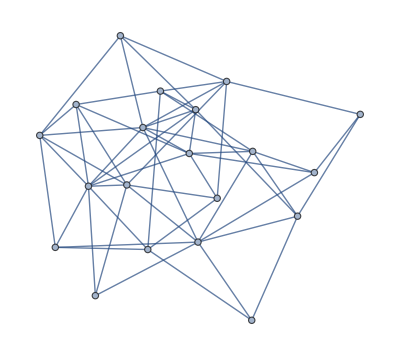

```mathematica
RandomGraph[{20,54}]
```

```mathematica
Indexed[x,#]&/@Range[20]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20}

```mathematica
VertexReplace[g,{Subscript[v, 1]->Subscript[w, 1],Subscript[v, 2]->Subscript[w, 2],…}]
```

```mathematica
VertexReplace[-Graphics-,Thread[Range[20]->(Indexed[v,#]&/@Range[20])]]
```

-Graphics-

```mathematica
Remove[RandomSymbolicWeightedMixedGraph]
```

```mathematica
{{RandomSymbolicWeightedMixedGraph[{vertices_,edges_},threshold_,randomFunction_,variablename_,options:OptionsPattern[]]/;0≤threshold≤1:=Block[{replaceCount,randomGraph},randomGraph=VertexReplace[RandomGraph[{vertices,edges},options],Thread[Range[20]->(Indexed[variablename,#]&/@Range[20])]];replaceCount=Floor[threshold edges];randomGraph=Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,randomGraph,RandomSample[EdgeList[randomGraph],replaceCount]]];Graph[randomGraph,EdgeWeight->(#1->randomFunction[]&)/@EdgeList[randomGraph]]]}, {}, {RandomSymbolicWeightedMixedGraph[{vertices_,edges_},threshold_,randomFunction_,variablename_,k_?IntegerQ,options:OptionsPattern[]]/;0≤threshold≤1:=Table[RandomSymbolicWeightedMixedGraph[{vertices,edges},threshold,randomFunction],k]}, {}, {RandomSymbolicWeightedMixedGraph[{vertices_,edges_},threshold_,randomFunction_,variablename_,array_List,options:OptionsPattern[]]/;0≤threshold≤1:=Array[RandomSymbolicWeightedMixedGraph[{vertices,edges},threshold,randomFunction]&,array]}, {}, {RandomSymbolicWeightedMixedGraph[graphDistribution_,threshold_,randomFunction_,,variablename_,options:OptionsPattern[]]/;0≤threshold≤1:=Block[{replaceCount,randomGraph},randomGraph=RandomGraph[graphDistribution,options];replaceCount=Floor[threshold EdgeCount[randomGraph]];randomGraph=Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,randomGraph,RandomSample[EdgeList[randomGraph],replaceCount]]];Graph[randomGraph,EdgeWeight->(#1->randomFunction[]&)/@EdgeList[randomGraph]]]}, {}, {RandomSymbolicWeightedMixedGraph[graphDistribution_,threshold_,randomFunction_,variablename_,k_?IntegerQ,options:OptionsPattern[]]/;0≤threshold≤1&&k≥1:=Table[RandomSymbolicWeightedMixedGraph[graphDistribution,threshold,randomFunction],k]}, {}, {RandomSymbolicWeightedMixedGraph[graphDistribution_,threshold_,randomFunction_,,variablename_,array_List,options:OptionsPattern[]]/;0≤threshold≤1:=Array[RandomSymbolicWeightedMixedGraph[graphDistribution,threshold,randomFunction]&,array]}}
```

{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}}

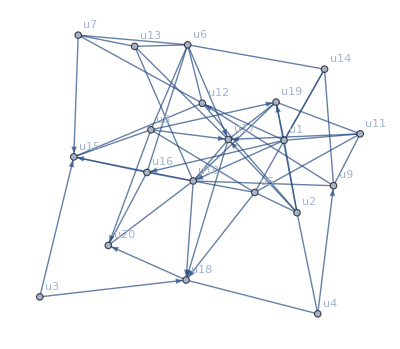

```mathematica
RandomSymbolicWeightedMixedGraph[{20,54},0.68,RandomReal[]&,u,VertexLabels->Automatic]
```

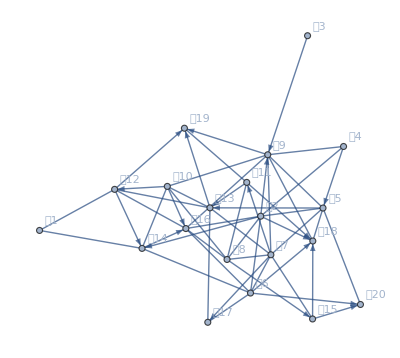

```mathematica
RandomSymbolicWeightedMixedGraph[{20,54},0.68,RandomReal[]&,𝒰,VertexLabels->Automatic]
```

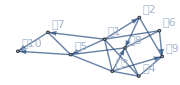

```mathematica
RandomSymbolicWeightedMixedGraph[{10,20},0.68,RandomReal[]&,𝒰,VertexLabels->Automatic,ImageSize->Small]
```